```mathematica
Fspring[s_]:=(b Em h^3 s)/(4 Ls^3)
```

```mathematica
Ls = 0.20;
h = 0.6*10^-3;
b=2.8*10^-2;
Em = 370*10^9;
M = M0/L0*Ls; (*масса колебающегося конца линейки*)
m = 0; (*масса грузика на конце линейки, при m=0 грузика нет и есть только собственные колебания линейки*)
l=0.24; (*удаление грузика от оси вращения*)
L0 = 1.03; (*длина всей линейки*)
M0 = 150.74*10^-3; (*масса всей линейки*)
```

```mathematica
Ioverall = (M Ls^2)/3+m l^2
```

0.000390265

```mathematica
solution = DSolve[{α''[t] == -(Fspring[α[t] * Ls] *Ls)/Ioverall, α[0] == 0.1, α'[0] ==0},α[t], t]
```

{{α[t]→0.1 Cos[84.6607 t]}}

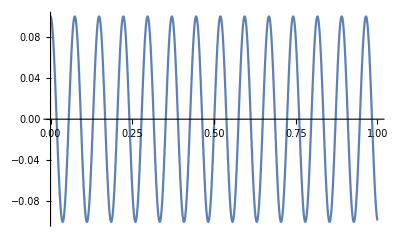

```mathematica
Plot[solution[[1, 1, 2]], {t, 0, 1}]
```

```mathematica
84.66/(2Pi)
```

13.4741

```mathematica
DSolve[{x''[t] == -(3Em b h^3)/(4M Ls^3) x[t], x[0] == 0.1, x'[0] == 0}, x[t], t]
DSolve[{x''[t] == -w x[t], x[0] == 0.1, x'[0] == 0}, x[t], t]
```

{{x[t]→0.1 Cos[13.5657 t]}}

{{x[t]→0.1 Cos[t √w]}}

```mathematica
14*2Pi//N
```

87.9646

```mathematica
Solve[√((3Ex b h^3)/(4M Ls^3)) == 88, Ex]
```

{{Ex→3.99764×10^11}}

## Поиск модуля Юнга

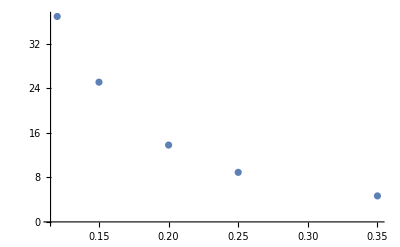

```mathematica
frequencies = {{0.25, 8.9}, {0.2, 13.8}, {0.15, 25.1}, {0.12, 36.9}, {0.35, 4.67}};
ListPlot[frequencies]
```

```mathematica
Manipulate[Show[ListPlot[frequencies], Plot[(√((3b h^3 *Ex L0)/(4M0 L^4)))/(2Pi), {L, 0, 0.40}]], {Ex, 0, 400*10^9}]
```

```mathematica
fit=FindFit[frequencies,(√((3 b Ex h^3 L0)/(4 M0 L^4)))/(2π),Ex,L]
```

{Ex→3.75163×10^11}

```mathematica
frequenciesForPlotting = Table[{Around[frequencies[[i, 1]], 0.01], Around[frequencies[[i,2]], 0.5]}, {i,1, Length@frequencies}]
```

{{0.2500.010,8.90.5},{0.2000.010,13.80.5},{0.1500.010,25.10.5},{0.1200.010,36.90.5},{0.3500.010,4.70.5}}

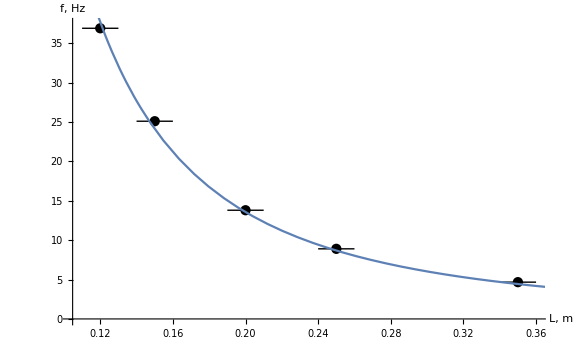

```mathematica
Show[
ListPlot[frequenciesForPlotting, AxesStyle->Directive[Black, 12], AxesLabel->{"L, m", "f, Hz"}, PlotStyle-> Black], 
Plot[√((3b h^3 *9.5*10^9)/(4(150.74*10^-3)/1.03*L* L^3)) , {L, 0, 0.40}], ImageSize -> Large]
```

```mathematica
Solve[√((3Ex b h^3)/(4(150.74*10^-3)/1.03)) == 0.5427137981478877, Ex]
```

{{Ex→9.50298×10^9}}

```mathematica
√((3b h^3 *9.5*10^9)/(4(150.74*10^-3)/1.03))
```

0.542629